#### Get component function (temporary)

```mathematica
Needs["Olveretal`"];
ClearAll[GetComponent]
Options[GetComponent]={Coordinates->"Spherical",Mute->True};
GetComponent[solvec_List,expr_List,layer_Integer,layout_List,n_Integer,OptionsPattern[]]:=
Block[{position,subdomain,nsubdomains,partition,zeroInDomain,startindex,listParity,listExtracted,(*options*) coordinates},

(* set up options *)
coordinates=OptionValue[Coordinates];
If[!OptionValue[Mute],
If[SameQ[coordinates,"Spheroidal"],Print["Spheroidal coordinates"],Print["Spherical coordinates"]]
];

(* recover subdomains from model *)
partition=Partition[Sort(*@Rest*)[Sprouts`domain],2,1];
nsubdomains=Length[partition];
Table[subdomain[i]=partition⟦i⟧,{i,1,Length[partition]}];
If[SameQ[N@First[subdomain[1]],0.],zeroInDomain=True,zeroInDomain=False];

(* find component position in solution vector *)
position=Flatten@Position[layout,Alternatives@@expr];

(* find parity of fields accross the origin based on their indices of spherical harmonics *)
listParity=
Block[{out},
If[zeroInDomain&&SameQ[layer,1],
Which[
SameQ[coordinates,"Spheroidal"],
Which[
MatchQ[#,f_[ℓ_,𝓂_]/;EvenQ[ℓ+𝓂]],out="even";,
MatchQ[#,f_[ℓ_,𝓂_]/;OddQ[ℓ+𝓂]],out="odd";,
True,Print["error with parity !"]
],
SameQ[coordinates,"Spherical"],
Which[
MatchQ[#,f_[ℓ_,𝓂_]/;EvenQ[ℓ]],out="even";,
MatchQ[#,f_[ℓ_,𝓂_]/;OddQ[ℓ]],out="odd";,
True,Print["error with parity !"];
],
True,Print["error with coordinates !"];
]
];
out
]&/@expr;

(* extracted elements from solution vector *)
listExtracted=
Block[{extracted},
If[zeroInDomain,
startindex=Max[(layer-3/2)*n*Length[layout]+1,1];
If[SameQ[layer,1],
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n/2-1⟧,{(#-1)*n/2+1,#*n/2}],
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n-1⟧,{(#-1)*n+1,#*n}]
],
startindex=(layer-1)*n*Length[layout]+1;
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n-1⟧,{(#-1)*n+1,#*n}]
]
]&/@position;

(* output: riffle with zeroes if zero is in first layer *)
If[zeroInDomain&&SameQ[layer,1],
Table[
Switch[listParity⟦i⟧,
"even",N@Riffle[listExtracted⟦i⟧,0.+0.ⅈ],
"odd",N@Riffle[listExtracted⟦i⟧,0.+0.ⅈ,{1,-1,2}],
True,Print["error with Riffle !"]
]
,{i,1,Length[expr]}],
N@listExtracted
]

]
```

Get::noopen: Cannot open Olveretal`.

Needs::nocont: Context Olveretal` was not created when Needs was evaluated.

# Compressible rotating Navier-Stokes

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["TenGSHui`","~/ownCloud/Shared/TenGSHui.m"];
Needs["spectral`","../spectral.m"];
Needs["sprouts`","../sprouts.m"];
```

Loading TenGSHui...

Done. Please execute DisplayPalette if you need the palette.

```mathematica
FastMode=True;
```

```mathematica
ℓmax=64;𝓂=0;ricb=0.35;
```

```mathematica
Rank[𝕦]^=1;
MaxDegree[𝕦]^=ℓmax;
𝕦[-1][ℓ_,𝓂_][r_]:=√((ℓ(ℓ+1))/2)((P[ℓ,𝓂][r])/r+P[ℓ,𝓂]'[r]-ⅈ T[ℓ,𝓂][r])
𝕦[0][ℓ_,𝓂_][r_]:=ℓ(ℓ+1)(P[ℓ,𝓂][r])/r
𝕦[1][ℓ_,𝓂_][r_]:=√((ℓ(ℓ+1))/2)((P[ℓ,𝓂][r])/r+P[ℓ,𝓂]'[r]+ⅈ T[ℓ,𝓂][r])
```

```mathematica
Rank[𝓈]^=0;
MaxDegree[𝓈]^=ℓmax;
𝓈[][ℓ_,𝓂_][r_]:=s[ℓ,𝓂][r]
```

```mathematica
ClearAll[lnρ]
lnρ[r_]:=(*0*)-6Log[r]
```

```mathematica
ClearAll[ρ]
Rank[ρ]^=0;
MaxDegree[ρ]^=0;
ρ[][ℓ_,𝓂_][r_]:=Exp[lnρ[r]]
```

```mathematica
Rank[invρ]^=0;
MaxDegree[invρ]^=0;
invρ[][ℓ_,𝓂_][r_]:=Exp[-lnρ[r]]
```

```mathematica
Rank[drS]^=0;
MaxDegree[drS]^=0;
drS[][ℓ_,𝓂_][r_]:=0
```

```mathematica
Rank[α]^=0;
MaxDegree[α]^=0;
α[][ℓ_,𝓂_][r_]:=1
```

```mathematica
Rank[T0]^=0;
MaxDegree[T0]^=0;
T0[][ℓ_,𝓂_][r_]:=r^6
```

```mathematica
Rank[invT0]^=0;
MaxDegree[invT0]^=0;
invT0[][ℓ_,𝓂_][r_]:=1/T0[][ℓ,𝓂][r]
```

```mathematica
Rank[κ]^=0;
MaxDegree[κ]^=0;
κ[][ℓ_,𝓂_][r_]:=1
```

```mathematica
ClearAll[g,gnorm]
gnorm=Integrate[ρ[][0,0][r],r];
g≡((-1)gnorm)⋆𝕖𝓇
```

```mathematica
𝕧≐invρ⊗𝕦
```

```mathematica
ClearAll[σ]
(*σ≐((ζ-2/3 μ)⋆𝕧)⊗𝕘)⊕(2μ)⋆(∇𝕧)*)
σ≐((-2/3 Ek)⋆ρ⊗(𝕧)⊗𝕘)⊕(2Ek⋆ρ)⊗(∇𝕧)
```

```mathematica
viscosity≐(σ)
```

```mathematica
buoyancy≐(-N2)⋆α⊗ρ⊗T0⊗g⊗𝓈
```

```mathematica
listpoleq=Table[Simplify[((λ⋆𝕦)⊕2⋆(𝟙[𝕫]𝕦)⊖viscosity⊕buoyancy)[0][ℓ,𝓂][r]],{ℓ,2,ℓmax,2}];
listtoreq=Table[Simplify[((λ⋆𝕦)⊕2⋆(𝟙[𝕫]𝕦)⊖viscosity⊕buoyancy)[0][ℓ,𝓂][r]],{ℓ,1,ℓmax,2}];
```

```mathematica
listenteq=Table[Simplify[((λ⋆(ρ⊗𝓈))⊕drS⊗(𝕖𝓇·𝕦)⊖invT0⊗((κ⊗ρ⊗∇𝓈)))[0][ℓ,𝓂][r]],{ℓ,2,ℓmax,2}];
```

```mathematica
listpol=Table[P[ℓ,𝓂],{ℓ,2,ℓmax,2}];
listtor=Table[T[ℓ,𝓂],{ℓ,1,ℓmax,2}];
lists=Table[s[ℓ,𝓂],{ℓ,2,ℓmax,2}];
```

```mathematica
ClearAll[listpolbc,listtorbc]
If[ricb==0,
listpolbc=Flatten[Table[{P[ℓ,𝓂][1],P[ℓ,𝓂]'[1]},{ℓ,2,ℓmax,2}]];
listtorbc=Flatten[Table[{T[ℓ,𝓂][1]},{ℓ,1,ℓmax,2}]];
listsbc=Flatten[Table[{s[ℓ,𝓂][1]},{ℓ,2,ℓmax,1}]];
,
listpolbc=Flatten[Table[{P[ℓ,𝓂][ricb],P[ℓ,𝓂]'[ricb],P[ℓ,𝓂][1],P[ℓ,𝓂]'[1]},{ℓ,2,ℓmax,2}]];
listtorbc=Flatten[Table[{T[ℓ,𝓂][ricb],T[ℓ,𝓂][1]},{ℓ,1,ℓmax,2}]];
listsbc=Flatten[Table[{s[ℓ,𝓂][ricb],s[ℓ,𝓂][1]},{ℓ,2,ℓmax,1}]];
];
```

```mathematica
ℒ=Join[listpoleq,listtoreq,listenteq];
𝒱=Join[listpol,listtor,lists];
ℬ=Join[listpolbc,listtorbc,listsbc];
```

```mathematica
Block[{Ek=10^-3,N2=-1},
A=SproutsFun[Join[ℒ,ℬ],𝒱,{r,ricb,1},68,eigenvalue->λ]
]
```

partition of the spatial domain :  {{0.35,1}}

eigenvalue problem of type :   (A0+A1 λ)x==0

Size of output matrices :  6528x6528

{SparseArray[<175202>, {6528, 6528}],SparseArray[<93250>, {6528, 6528}]}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/rekierj/sprouts/examples

```mathematica
Export["../slepc/A0.mtx",A[[1]]]
Export["../slepc/A1.mtx",A[[2]]]
```

../slepc/A0.mtx

../slepc/A1.mtx

```mathematica
(*Export["../A.mtx",A[[1]]]
Export["../B.mtx",-A[[2]]]*)
```

../A.mtx

../B.mtx

## Solve and post-process

```mathematica
SetDirectory[NotebookDirectory[]];
Reeigv=Import["../slepc/Real_Eigenvec.dat"];
Imeigv=Import["../slepc/Imag_Eigenvec.dat"];
eigv=(*Most@*)(Reeigv+I Imeigv)ᵀ;
eig=Import["../slepc/eigenvalues.dat"];
eig=Table[eig[[i,1]]+I eig[[i,2]],{i,1,Length[eig]}];
```

```mathematica
pos=1;
```

```mathematica
(* extract components from solution *)
ClearAll[out,outnull]
Block[{list,coef,assoc=<||>},
Table[
list[layer]=Sprouts`layout⟦layer⟧;
coef[layer]=Chop@GetComponent[eigv⟦pos⟧,list[layer],layer,Sprouts`layout⟦layer⟧,Sprouts`nr];
AppendTo[assoc,AssociationThread[list[layer],coef[layer]]]
,{layer,1,Sprouts`nlayers}];
out=assoc;
]
outnull=Map[(#)->ConstantArray[0,Sprouts`nr]&,Keys[out]/.f_[ℓ_,𝓂_]->f[ℓ-1,𝓂]]~Join~Map[(#)->ConstantArray[0,Sprouts`nr]&,Keys[out]/.f_[ℓ_,𝓂_]->f[ℓ+1,𝓂]];
AppendTo[out,outnull];
```

```mathematica
ClearAll[NChebevalC]
NChebevalC[c_][x_]:=NChebeval[N[Re[c]]][x]+ⅈ NChebeval[N[Im[c]]][x]
xk=Cos[((2Range[1,Sprouts`nr]-1)π)/(2Sprouts`nr)]//N;
rk=Sprouts`rfu[1][xk];
```

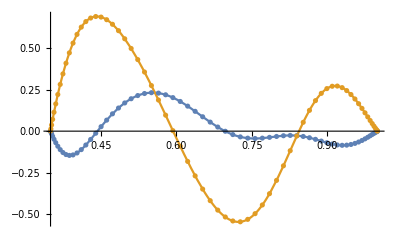

```mathematica
(* plot chosen component *)
data=NChebevalC[T[1,0]/.out][xk];
interp=Interpolation[{rk,data}ᵀ];
Show[Plot[{Re[interp[r]],Im[interp[r]]},{r,Min[rk],1},PlotRange->{{Min[rk],1},All}],ListPlot[{{rk,Re[data]}ᵀ,{rk,Im[data]}ᵀ}]]
```

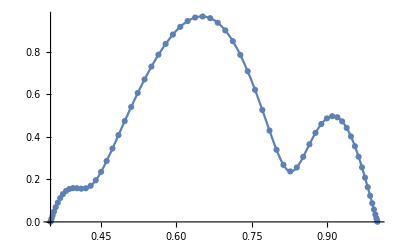

```mathematica
(* plot chosen component *)
data=NChebevalC[T[3,0]/.out][xk];
interp=Interpolation[{rk,data}ᵀ];
Show[Plot[Abs[interp[r]],{r,Min[rk],1},PlotRange->{{Min[rk],1},All}],ListPlot[{{rk,Abs[data]}ᵀ}]]
```

```mathematica
ClearAll[up,ut,upint,utint,urint,ucint,upintconj,ucintconj,urintconj,utintconj,uout,entropy]
gridr=N@Subdivide[Sequence@@Sprouts`layer[1],100];
Block[{mode=pos,ℓ,𝓂,head,subset=Sprouts`layout⟦1⟧,listcomp,comp},
listcomp=GetComponent[(*solution*)eigv⟦mode⟧,subset,1,Sprouts`layout⟦1⟧,Sprouts`nr,Coordinates->"Spherical"];
Table[
head=Head[subset⟦i⟧];ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
comp=listcomp⟦i⟧;
Which[
SameQ[head,P],
up[ℓ,𝓂]=((Function[x,(NChebeval[Re@N@#][Sprouts`ufr[1][x]]+ⅈ NChebeval[N@Im@#][Sprouts`ufr[1][x]])]/@gridr)&@comp);
upint[ℓ,𝓂]=Interpolation[{gridr,up[ℓ,𝓂]}ᵀ];
upintconj[ℓ,𝓂]=Interpolation[{gridr,up[ℓ,𝓂]*}ᵀ];
urint[ℓ,𝓂]=Evaluate[(ℓ(ℓ+1))/# upint[ℓ,𝓂][#]]&;
urintconj[ℓ,𝓂]=Evaluate[(ℓ(ℓ+1))/# upintconj[ℓ,𝓂][#]]&;
ucint[ℓ,𝓂]=Evaluate[(upint[ℓ,𝓂][#])/#+upint[ℓ,𝓂]'[#]]&;
ucintconj[ℓ,𝓂]=Evaluate[(upintconj[ℓ,𝓂][#])/#+upintconj[ℓ,𝓂]'[#]]&,
SameQ[head,T],
ut[ℓ,𝓂]=((Function[x,(NChebeval[Re@N@#][Sprouts`ufr[1][x]]+ⅈ NChebeval[N@Im@#][Sprouts`ufr[1][x]])]/@gridr)&@comp);
utint[ℓ,𝓂]=Interpolation[{gridr,ut[ℓ,𝓂]}ᵀ];
utintconj[ℓ,𝓂]=Interpolation[{gridr,ut[ℓ,𝓂]*}ᵀ]
];
uout[-1][ℓ,𝓂]=Evaluate[√((ℓ(ℓ+1))/2)(ucint[ℓ,𝓂][#]-ⅈ utint[ℓ,𝓂][#])]&;uout[0][ℓ,𝓂]=Evaluate[urint[ℓ,𝓂][#]]&;uout[+1][ℓ,𝓂]=Evaluate[√((ℓ(ℓ+1))/2)(ucint[ℓ,𝓂][#]+ⅈ utint[ℓ,𝓂][#])]&;

,{i,1,Length[subset]}]
];
```

```mathematica
utint[ℓ_,𝓂_][r_]:=0;
urint[ℓ_,𝓂_][r_]:=0;
ucint[ℓ_,𝓂_][r_]:=0;
upint[ℓ_,𝓂_][r_]:=0;
utintconj[ℓ_,𝓂_][r_]:=0;
urintconj[ℓ_,𝓂_][r_]:=0;
ucintconj[ℓ_,𝓂_][r_]:=0;
upintconj[ℓ_,𝓂_][r_]:=0;
```

```mathematica
ClearAll[Y]
Y[ℓ_,𝓂_,θ_,ϕ_]:=Y[ℓ,𝓂,θ,ϕ]=√((4π)/(2 ℓ+1))SphericalHarmonicY[ℓ,𝓂,θ,ϕ]
```

```mathematica
gridθ=Range[0.,π,π/100];
Block[{ℓ,𝓂,subset=Sprouts`layout⟦1⟧,ϕ=0},
gridur=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
Re@Which[
SameQ[{ℓ,𝓂},{0,0}],uout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ],
SameQ[𝓂,0],uout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ],
True,2*uout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ]
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
griduθ=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
(√2)/2 Re@Which[
SameQ[{ℓ,𝓂},{0,0}],0.+ⅈ 0.,
SameQ[𝓂,0],uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]-uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ],
True,2(uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]-uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ])
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
griduϕ=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
(√2)/2 Im@Which[
SameQ[{ℓ,𝓂},{0,0}],0.+ⅈ 0.,
SameQ[𝓂,0],uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]+uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ],
True,2(uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]+uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ])
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
];
griduρ=(gridurᵀ*Sin[gridθ]+griduθᵀ*Cos[gridθ])ᵀ;
griduz=(gridurᵀ*Cos[gridθ]-griduθᵀ*Sin[gridθ])ᵀ;
```

```mathematica
coord[r_,θ_,ϕ_]:=
{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ] };
ClearAll[StreamMeridPlot,MeridPlot]
StreamMeridPlot[rj_List,θk_List,ϕ_,{v1_,v2_,s_},opts___]:=
Module[{nr=Length[rj],nθ=Length[θk],tab,max=If[Max@Abs[s]≠0,Max@Abs[s],1]},
tab=Flatten[Table[{{Sign[rj⟦j⟧] √((coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦1⟧)^2+(coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦2⟧)^2),coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦3⟧},{{v1⟦j,k⟧,v2⟦j,k⟧},s⟦j,k⟧}},{j,1,nr},{k,1,nθ}],1];
tab;
ListStreamDensityPlot[tab,ColorFunction->(Lighter[ColorData[(*"LakeColors"*)"RedBlueTones"][Rescale[#,{-max,max} ]],0.1]&),ColorFunctionScaling->False,opts]]
coord[r_,θ_,ϕ_]:=
{Abs[r] Cos[ϕ] Sin[θ],Abs[r] Sin[θ] Sin[ϕ],Abs[r] Cos[θ] };
MeridPlot[rj_List,θk_List,mat_,ϕ_,opts___]:=
Module[{nr=Length[rj],nθ=Length[θk],tab,max=If[Max@Abs[mat]≠0,Max@Abs[mat],1]},
tab=Flatten[Table[{Sign[rj⟦j⟧] √((coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦1⟧)^2+(coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦2⟧)^2),coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦3⟧,mat⟦j,k⟧},{j,1,nr},{k,1,nθ}],1];
ListContourPlot[tab,ColorFunction->(ColorData[(*"SunsetColors"*)"RedBlueTones"][Rescale[#,{-1.25max,1.25max} ]]&),ColorFunctionScaling->False,opts]]
```

```mathematica
<<MaTeX`
```

```mathematica
Show[
GraphicsRow[{
MeridPlot[gridr,gridθ,gridur,0,AspectRatio->2,PlotRangePadding->None,Frame->False,Contours->50,PlotRange->All,ContourStyle->None,RegionFunction->Function[{x,y,z},First[Sprouts`domain]<Norm[{x,y}]<Last[Sprouts`domain]],PlotLabel->MaTeX["u^r",Magnification->2]],MeridPlot[gridr,gridθ,griduθ,0,AspectRatio->2,PlotRangePadding->None,Frame->False,Contours->50,PlotRange->All,ContourStyle->None,RegionFunction->Function[{x,y,z},First[Sprouts`domain]<Norm[{x,y}]<Last[Sprouts`domain]],PlotLabel->MaTeX["u^\\theta",Magnification->2]],
MeridPlot[gridr,gridθ,griduϕ,0,AspectRatio->2,PlotRangePadding->None,Frame->False,Contours->50,PlotRange->All,ContourStyle->None,RegionFunction->Function[{x,y,z},First[Sprouts`domain]<Norm[{x,y}]<Last[Sprouts`domain]],PlotLabel->MaTeX["u^\\varphi",Magnification->2]],
StreamMeridPlot[gridr,gridθ,0,{griduρ,griduz,griduϕ},AspectRatio->2,PlotRangePadding->None,Frame->False,PlotRange->All,StreamScale->Medium,StreamColorFunction->None,StreamStyle->Black,RegionFunction->Function[{x,y,z},First[Sprouts`domain]<Norm[{x,y}]<Last[Sprouts`domain]],PlotLabel->MaTeX["\\mathbf{u}",Magnification->2]]
},ImageSize->Full],PlotLabel->MaTeX[λ==Chop@N[eig⟦pos⟧,5](*MaTeX["\\lambda="<>ToString[Chop@N[eig⟦pos⟧,5]]*),Magnification->1.5]]
```

-Graphics-